```mathematica
SetDirectory[NotebookDirectory[]];
```

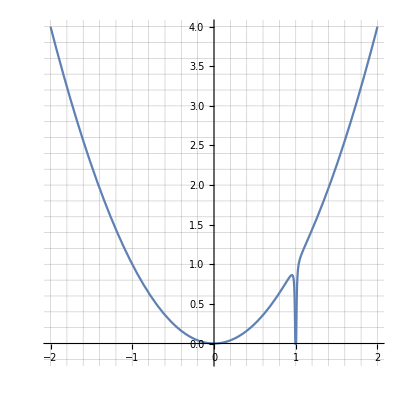

```mathematica
solver1=Plot[
x^2+Exp[-1/(100*(x-1))^2]-1,
{x,-2,2},
PlotRange->{{-2,2},{-0.2,4}},
GridLines->{Range[-2,2,0.2],Range[-1,4,0.2]},
LabelStyle->{FontFamily->"Andale Mono",FontSize->14},
AspectRatio->1,
PlotRangeClipping->False,
ImageSize->{400,Automatic}
]
```

```mathematica
solver2=Plot3D[
Sin[x]+y^2,
{x,-2,2},
{y,-2,2},
ColorFunction->Function[{x,y,z},ColorData["Rainbow"][z]],
ViewPoint->{-1.3, -1.4, 0.25},
LabelStyle->{FontFamily->"Andale Mono",FontSize->14},
ImageSize->{400,Automatic},
AxesLabel->{"x","y","z"}
]
```

-Graphics3D-

```mathematica
solver3=ContourPlot3D[
x+y^2+z,
{x,-2,2},
{y,-2,2},
{z,-2,2},
ColorFunction->Function[{x,y,z,f},{Opacity[0.75],ColorData["Rainbow"][f]}],
Contours->20,
Mesh->None,
ViewPoint->{-3.3, -2.4, 2.},
LabelStyle->{FontFamily->"Andale Mono",FontSize->14},
AxesLabel->{"x","y","z"},
ImageSize->{400,Automatic}
]
```

-Graphics3D-

```mathematica
Export["example_1.png",solver1];
Export["example_2.png",solver2];
Export["example_3.png",solver3];
```